## Project 2 - Neyman-Pearson Region

### Overview

The goal is to estimate the Neyman-Pearson Region for two distributions by estimating and plotting the supporting lines of the region.

Steps for Estimating the Neyman-Pearson Region
1. Specify distributions p, q
2. Specify mixture parameter 0 ≤ t ≤ 1
3. Specify number of mixture distribution samples N
4. Generate N samples X from mixture distribution tp+(1-t)q
5. Calculate p(x) and q(x) for each x∈X
6. Specify number of supporting lines M
7. Generate M pairs Y: (u,v) with u,v ≥ 0
8. Calculate ρ(u,v) for each (u,v)∈Y using all x∈X
	ρ(u,v)=v-∫_Ω (vq(x)-up(x))_+ⅆμ(x)
	    =v-∫_Ω (tp(x)+(1-t)q(x)) ((vq(x)-up(x))_+)/(tp(x)+(1-t)q(x))ⅆμ(x)
                =v-E_(tp(x)+(1-t)q(x))[((vq(x)-up(x))_+)/(tp(x)+(1-t)q(x))]	
9. Plot M supporting lines: uα+vβ=ρ(u,v) for each (u,v)∈Y

### Functions

```mathematica
xMixtureSamples[xDistP_,xDistQ_,iSamples_,nT_]:=Block[{vSamples},
vSamples=RandomVariate[MixtureDistribution[{nT,(1-nT)},{xDistP,xDistQ}],iSamples];
Map[{PDF[xDistP,#],PDF[xDistQ,#],nT*PDF[xDistP,#]+(1-nT)*PDF[xDistQ,#],#}&,vSamples]
]
xGenerateUV[iPairs_]:=Block[{},
Transpose@{Table[x,{x,0.001,.999,1/iPairs}],Reverse@Table[x,{x,0.001,.999,1/iPairs}]}
]
xPos[nVal_]:=Block[{},
0.5(nVal+Abs@nVal)
]
xCalcRho[mSamples_,{nU_,nV_},bCorr_]:=Block[{vRhoEst},
vRhoEst=Map[(xPos[nV*#[[2]]-nU*#[[1]]]/(#[[3]]))&,mSamples];
{nU,nV,nV-Mean@vRhoEst,StandardDeviation@vRhoEst/Sqrt[Length@mSamples],If[bCorr,N@Correlation[vRhoEst,mSamples[[All,3]]],Nothing]}
]
xCalcIntersect[vUVRho1_,vUVRho2_]:=Block[{nα},
nα=(vUVRho2[[2]]*vUVRho1[[3]]-vUVRho1[[2]]*vUVRho2[[3]])/(vUVRho1[[1]]*vUVRho2[[2]]-vUVRho1[[2]]*vUVRho2[[1]]);
{nα,(vUVRho1[[3]]-vUVRho1[[1]]*nα)/vUVRho1[[2]]}
]
xPlotLines[mUVRho_,cColor_,sLegend_]:=Block[{mXYInts,mPoints={},nYIntHigh=0,vPoint1,vPoint2},
(*Sort all lines by decreasing x-intercept*)
mXYInts=Map[{#[[3]]/#[[1]],#[[3]]/#[[2]],#}&,mUVRho];
mXYInts=Sort[mXYInts,#1[[1]]≥#2[[1]]&];

(*Keep only the lines that contribute to generating the bound*)
(*Lines with x-intercept > 1 can't be tangent to the bound. Use 1.01 to allow for some flexibility*)
For[i=1,i<=Length@mXYInts,i++,
AppendTo[mPoints,
If[mXYInts[[i,1]]≤1.01&& mXYInts[[i,2]]≥nYIntHigh,
nYIntHigh=mXYInts[[i,2]]; mXYInts[[i]],
Nothing
]
]];

(*Find the points of intersection among the lines that generate the bound*)
If[Length@mPoints>1,
mXYInts={{{mPoints[[1,1]],0},xCalcIntersect[mPoints[[1,3]],mPoints[[2,3]]]}};
For[i=2,i<Length@mPoints,i++,
AppendTo[mXYInts,
{mXYInts[[i-1,2]],xCalcIntersect[mPoints[[i,3]],mPoints[[i+1,3]]]}
]];
AppendTo[mXYInts,{mXYInts[[-1,2]],{0,mPoints[[-1,2]]}}];,
mXYInts={{{mPoints[[1,1]],0},{0,mPoints[[1,2]]}}};
];

{ListLinePlot[mXYInts,PlotStyle->cColor,AxesLabel->{"α","β"},PlotRange->{{0,1},{0,1}},PlotLegends->Placed[{sLegend},Below],ImageSize->{400,300}],mPoints}
]
```

### Estimated Neyman-Pearson Region for 2 Normal Distributions

#### Parameters and Functions

Samples are drawn from mixture distribution with weights 0.5 and 0.5 (the nT parameter).

```mathematica
iNormalMixtureSamples=10000;
iNormalUVPairs=50;

xNPR2Normal[vPDistParam_,vQDistParam_,nT_,bCorr_]:=Block[{mSamples,mUVRho},
mSamples=xMixtureSamples[NormalDistribution[vPDistParam[[1]],vPDistParam[[2]]],NormalDistribution[vQDistParam[[1]],vQDistParam[[2]]],iNormalMixtureSamples,nT];
mUVRho=Map[xCalcRho[mSamples,#,bCorr]&,xGenerateUV[iNormalUVPairs]];
{xPlotLines[mUVRho,Blue,"N"<> ToString@vPDistParam<> ",N"<>ToString@vQDistParam],mUVRho[[All,4]]} (*{plot, plot line values}, all standard deviations*)
]
```

#### Sanity Check - N(0,1) and N(0,1)

It is impossible to tell the difference between two distributions that are the same. So, the estimated Neyman-Pearson region should be the line of ignorance (i.e. the line between (0,1) and (1,0).

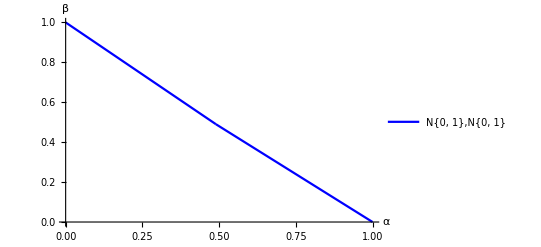
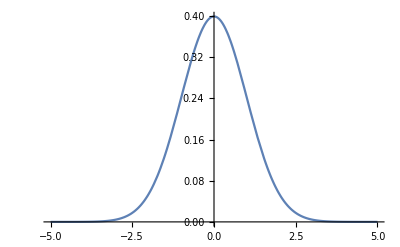

```mathematica
Row[{xNPR2Normal[{0,1},{0,1},0.5,False][[1,1]],
Plot[PDF[NormalDistribution[0,1],x],{x,-5,5},ImageSize->{400,300}]}]
```

#### N(0,1) and N(0,3)

If the number of mixture samples is too low, the estimation does not reliably generate the entire Neyman-Pearson lower bound. In particular, the part of the bound with α or β close to 1 is not included in the estimation. If the number of tangent lines is too low, the Neyman-Pearson lower bound is misrepresented as a piecewise linear function. Visually, it looks like a polygon, when in reality it is a curve (at least in this example). 10000 mixture sample and 50 tangent lines provides a reliable estimation, though this may be too conservative.

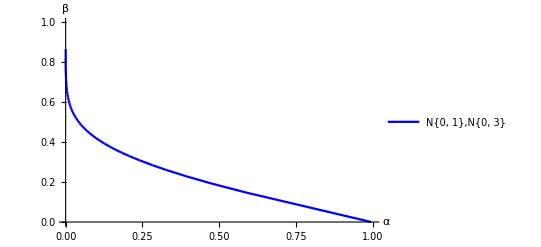
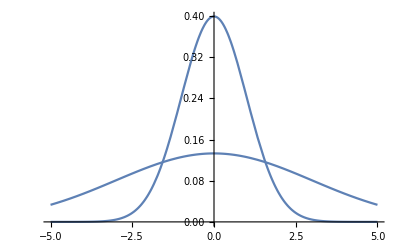

```mathematica
{{pNPRNormalPlot,vNPRNormalPlotLineValues},vNPRNormalSDs}=xNPR2Normal[{0,1},{0,3},0.5,True];
Row[{pNPRNormalPlot,
Show[Plot[PDF[NormalDistribution[0,1],x],{x,-5,5},ImageSize->{400,300}],Plot[PDF[NormalDistribution[0,3],x],{x,-5,5},ImageSize->{400,300}]]}]
```

### Estimated Neyman-Pearson Region for 2 Laplace Distributions

#### Parameters and Functions

Samples are drawn from mixture distribution with weights 0.5 and 0.5 (the nT parameter).

```mathematica
iLaplaceMixtureSamples=10000;
iLaplaceUVPairs=50;

xNPR2Laplace[vPDistParam_,vQDistParam_,nT_]:=Block[{mSamples,mUVRho},
mSamples=xMixtureSamples[LaplaceDistribution[vPDistParam[[1]],vPDistParam[[2]]],LaplaceDistribution[vQDistParam[[1]],vQDistParam[[2]]],iLaplaceMixtureSamples,nT];
mUVRho=Map[xCalcRho[mSamples,#,False]&,xGenerateUV[iLaplaceUVPairs]];
{xPlotLines[mUVRho,Red,"Laplace"<> ToString@vPDistParam<> ",Laplace"<>ToString@vQDistParam],mUVRho[[All,4]]} (*{plot, plot line values}, all standard deviations*)
]
```

#### Sanity Check - Laplace(0,1) and Laplace(0,1)

It is impossible to tell the difference between two distributions that are the same. So, the estimated Neyman-Pearson region should be the line of ignorance (i.e. the line between (0,1) and (1,0).

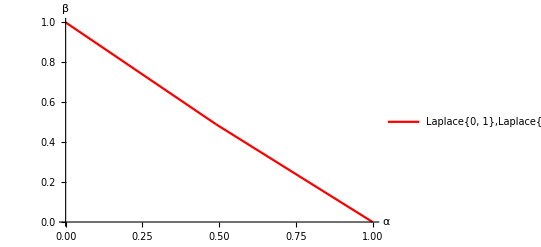
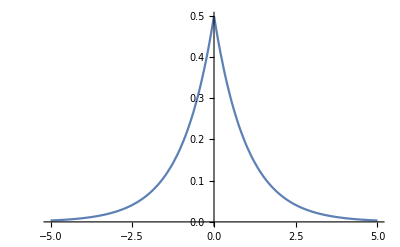

```mathematica
Row[{xNPR2Laplace[{0,1},{0,1},0.5][[1,1]],
Plot[PDF[LaplaceDistribution[0,1],x],{x,-5,5},ImageSize->{400,300}]}]
```

#### Laplace(0,1) and Laplace(0,3)

If the number of mixture samples is too low, the estimation does not reliably generate the entire Neyman-Pearson lower bound. In particular, the part of the bound with α or β close to 1 is not included in the estimation. If the number of tangent lines is too low, the Neyman-Pearson lower bound is misrepresented as a piecewise linear function. Visually, it looks like a polygon, when in reality it is a curve (at least in this example). 10000 mixture sample and 50 tangent lines provides a reliable estimation, though this may be too conservative.

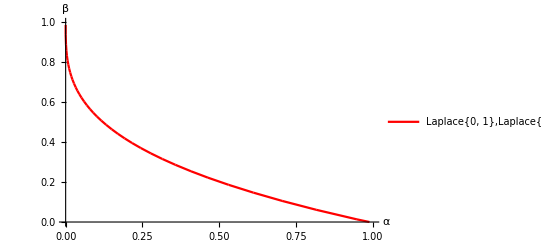
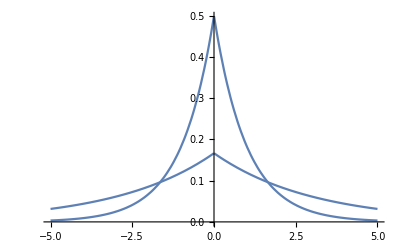

```mathematica
{{pNPRLaplacePlot,vNPRLaplacePlotLineValues},vNPRLaplaceSDs}=xNPR2Laplace[{0,1},{0,3},0.5];
Row[{pNPRLaplacePlot,
Show[Plot[PDF[LaplaceDistribution[0,1],x],{x,-5,5},ImageSize->{400,300}],Plot[PDF[LaplaceDistribution[0,3],x],{x,-5,5},ImageSize->{400,300}]]}]
```

### Estimated Neyman-Pearson Region for 2 Cauchy Distributions

#### Parameters and Functions

Samples are drawn from mixture distribution with weights 0.5 and 0.5 (the nT parameter).

```mathematica
iCauchyMixtureSamples=10000;
iCauchyUVPairs=50;

xNPR2Cauchy[vPDistParam_,vQDistParam_,nT_]:=Block[{mSamples,mUVRho},
mSamples=xMixtureSamples[CauchyDistribution[vPDistParam[[1]],vPDistParam[[2]]],CauchyDistribution[vQDistParam[[1]],vQDistParam[[2]]],iCauchyMixtureSamples,nT];
mUVRho=Map[xCalcRho[mSamples,#,False]&,xGenerateUV[iCauchyUVPairs]];
{xPlotLines[mUVRho,Green,"Cauchy"<> ToString@vPDistParam<> ",Cauchy"<>ToString@vQDistParam],mUVRho[[All,4]]} (*{plot, plot line values}, all standard deviations*)
]
```

#### Sanity Check - Cauchy(0,1) and Cauchy(0,1)

It is impossible to tell the difference between two distributions that are the same. So, the estimated Neyman-Pearson region should be the line of ignorance (i.e. the line between (0,1) and (1,0).

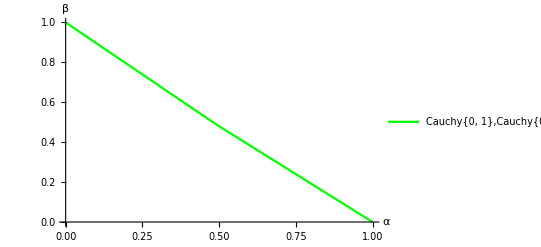
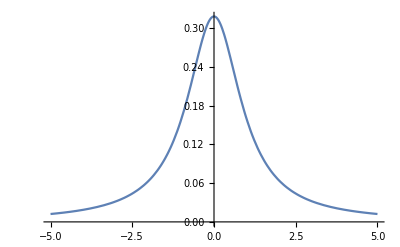

```mathematica
Row[{xNPR2Cauchy[{0,1},{0,1},0.5][[1,1]],
Plot[PDF[CauchyDistribution[0,1],x],{x,-5,5},ImageSize->{400,300}]}]
```

#### Cauchy(0,1) and Cauchy(0,3)

If the number of mixture samples is too low, the estimation does not reliably generate the entire Neyman-Pearson lower bound. In particular, the part of the bound with α or β close to 1 is not included in the estimation. If the number of tangent lines is too low, the Neyman-Pearson lower bound is misrepresented as a piecewise linear function. Visually, it looks like a polygon, when in reality it is a curve (at least in this example). 10000 mixture sample and 50 tangent lines provides a reliable estimation, though this may be too conservative.

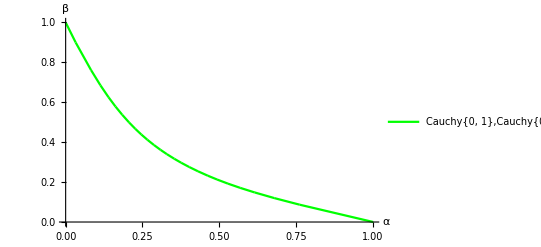
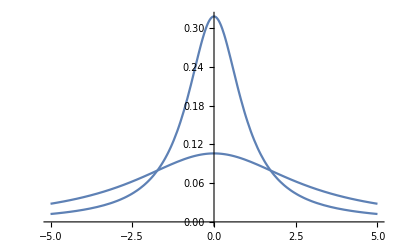

```mathematica
{{pNPRCauchyPlot,vNPRCauchyPlotLineValues},vNPRCauchySDs}=xNPR2Cauchy[{0,1},{0,3},0.5];
Row[{pNPRCauchyPlot,
Show[Plot[PDF[CauchyDistribution[0,1],x],{x,-5,5},ImageSize->{400,300}],Plot[PDF[CauchyDistribution[0,3],x],{x,-5,5},ImageSize->{400,300}]]}]
```

### Comparison

Overlaying the 3 graphs, you can see the relationship between the three Neyman-Pearson lower bounds. For lower values of α, the bound for the Normal lies below the bound for the Laplace which lies below the bound for the Cauchy. As α increases, the bounds overlap. In terms of classification tests, for lower values of α (less than approximately 0.4), the distinction among the best tests is clear. The best test for a given low α under Normal classification has lower β than the best test for Laplace classification, and the same applies for Laplace relative to Cauchy. For higher α, the distinction is not clear, shown by the overlap of the curves. So, the best tests for classification at higher α perform similarly among all three classifications.

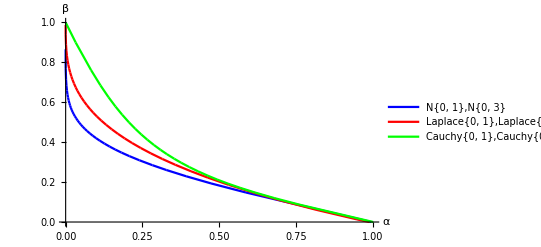

```mathematica
Show[pNPRNormalPlot,pNPRLaplacePlot,pNPRCauchyPlot]
```

### Sample Size and Error (Standard Deviations) For ρ(u,v) Estimates

10000 mixture samples and 50 (u,v) pairs are generated for each Neyman-Pearson lower bound estimation. Given a (u,v) pair, Monte Carlo simulation is used to estimate ρ(u,v) as an expected value of many ρ(u,v) estimates (see Overview). In theory, every (u,v) pair should generate a line that is tangent to the Neyman-Pearson lower bound. However, some generated “tangent” lines are not actually tangent to the bound. This isn’t surprising, since ρ(u,v) is being estimated. See Functions, xPlotLines[]. A slight tolerance is allowed for tangent lines with x-intercept > 1.

```mathematica
Grid[{{"NP Lower Bound","Mixture Samples","UV Pairs","# Tangent Lines"},
{"Normal",iNormalMixtureSamples,iNormalUVPairs,Length@vNPRNormalPlotLineValues},
{"Laplace",iLaplaceMixtureSamples,iLaplaceUVPairs,Length@vNPRLaplacePlotLineValues},
{"Cauchy",iCauchyMixtureSamples,iCauchyUVPairs,Length@vNPRCauchyPlotLineValues}},Dividers->All]
```

NP Lower Bound | Mixture Samples | UV Pairs | # Tangent Lines
Normal | 10000 | 50 | 37
Laplace | 10000 | 50 | 38
Cauchy | 10000 | 50 | 37

The standard deviation will be different, depending on the values of u,v and how the (x)_+ function evaluates for each mixture distribution sample. The standard deviations are given in the grids below. In all cases, the standard deviations are low compared to the means. Also, notice that the entries are in order of decreasing standard deviation. However, they were actually sorted in order of decreasing x-intercept (see Functions, xPlotLine[]). So, for the more horizontally oriented tangent lines, the individual ρ(u,v) estimates for each mixture sample were less precise overall. For the Cauchy bound, it looks like the more vertically oriented tangent line ρ(u,v) estimates all evaluated to the value of v; the expected value estimate was 0.

```mathematica
Row[{Grid[Join[{{"Normal Tangent ρ(u,v)",SpanFromLeft},{"Mean ρ(u,v)","Std. Dev.","X-Int"}},Map[Flatten@#&,vNPRNormalPlotLineValues][[All,{5,6,1}]]],Dividers->All]," ",
Grid[Join[{{"Laplace Tangent ρ(u,v)",SpanFromLeft},{"Mean ρ(u,v)","Std. Dev.","X-Int"}},Map[Flatten@#&,vNPRLaplacePlotLineValues][[All,{5,6,1}]]],Dividers->All]," ",
Grid[Join[{{"Cauchy Tangent ρ(u,v)",SpanFromLeft},{"Mean ρ(u,v)","Std. Dev.","X-Int"}},Map[Flatten@#&,vNPRCauchyPlotLineValues][[All,{5,6,1}]]],Dividers->All]
}]
```

Normal Tangent ρ(u,v) |  | 
Mean ρ(u,v) | Std. Dev. | X-Int
0.259912 | 0.00541931 | 0.995833
0.268709 | 0.0053264 | 0.956258
0.274309 | 0.00521191 | 0.911327
0.277579 | 0.00508364 | 0.864733
0.278923 | 0.00494505 | 0.817955
0.278882 | 0.00480031 | 0.772526
0.277501 | 0.00464979 | 0.72835
0.275052 | 0.00449534 | 0.685916
0.271735 | 0.00433827 | 0.645452
0.267702 | 0.00417958 | 0.607034
0.263011 | 0.00401962 | 0.570523
0.25769 | 0.00385853 | 0.535738
0.251761 | 0.00369638 | 0.502516
0.245353 | 0.00353392 | 0.470928
0.238468 | 0.00337113 | 0.440791
0.231181 | 0.00320844 | 0.412088
0.22347 | 0.0030457 | 0.384631
0.215374 | 0.00288311 | 0.358359
0.206927 | 0.00272085 | 0.333216
0.198158 | 0.00255908 | 0.309138
0.189111 | 0.00239813 | 0.286098
0.17973 | 0.00223772 | 0.26392
0.170023 | 0.00207788 | 0.242543
0.160012 | 0.00191875 | 0.22193
0.14971 | 0.00176042 | 0.202037
0.139138 | 0.00160307 | 0.182836
0.128308 | 0.00144688 | 0.164287
0.117209 | 0.00129196 | 0.146329
0.105836 | 0.00113846 | 0.128911
0.0941687 | 0.000986543 | 0.111972
0.0821813 | 0.000836366 | 0.0954487
0.0698541 | 0.00068815 | 0.0792895
0.0571813 | 0.000542402 | 0.0634642
0.0440853 | 0.00039961 | 0.0478667
0.0304824 | 0.000260534 | 0.0323937
0.0162535 | 0.000126857 | 0.0169131
0.000865624 | 4.80389×10^-6 | 0.000882389 Laplace Tangent ρ(u,v) |  | 
Mean ρ(u,v) | Std. Dev. | X-Int
0.238534 | 0.00451094 | 0.989769
0.257249 | 0.00449743 | 0.985627
0.272351 | 0.00444881 | 0.96922
0.284347 | 0.00437416 | 0.944673
0.29363 | 0.00427974 | 0.914736
0.300532 | 0.00417018 | 0.881327
0.305358 | 0.0040492 | 0.845868
0.308444 | 0.00392024 | 0.809564
0.309856 | 0.00378437 | 0.772709
0.309837 | 0.0036437 | 0.735955
0.30851 | 0.00349941 | 0.69957
0.305986 | 0.00335239 | 0.663744
0.302408 | 0.00320374 | 0.628707
0.297876 | 0.00305418 | 0.594563
0.292434 | 0.00290409 | 0.561293
0.286152 | 0.00275396 | 0.528932
0.279046 | 0.00260388 | 0.497407
0.271202 | 0.00245437 | 0.466785
0.262669 | 0.00230572 | 0.437054
0.253535 | 0.00215842 | 0.408269
0.243835 | 0.0020128 | 0.380398
0.233524 | 0.0018687 | 0.35329
0.222653 | 0.00172639 | 0.32695
0.211225 | 0.00158594 | 0.301319
0.199304 | 0.00144769 | 0.276427
0.186916 | 0.0013119 | 0.252249
0.17408 | 0.00117886 | 0.228751
0.160744 | 0.00104853 | 0.205818
0.146923 | 0.000921021 | 0.183424
0.132703 | 0.000796939 | 0.161636
0.118022 | 0.00067645 | 0.140336
0.10289 | 0.000559927 | 0.1195
0.0873002 | 0.000447882 | 0.0990921
0.0712152 | 0.000340884 | 0.0790401
0.0546411 | 0.000239689 | 0.059328
0.0375297 | 0.000146069 | 0.0398828
0.0197523 | 0.000063587 | 0.0205539
0.000987401 | 1.39328×10^-6 | 0.00100652 Cauchy Tangent ρ(u,v) |  | 
Mean ρ(u,v) | Std. Dev. | X-Int
0.261568 | 0.00355648 | 1.00218
0.275089 | 0.00347513 | 0.978963
0.286278 | 0.0033697 | 0.951091
0.295643 | 0.00324769 | 0.921005
0.303593 | 0.0031147 | 0.890301
0.310324 | 0.00297358 | 0.859623
0.315933 | 0.00282584 | 0.829219
0.320561 | 0.00267348 | 0.799404
0.324103 | 0.00251587 | 0.769841
0.326648 | 0.00235424 | 0.740698
0.328233 | 0.00218935 | 0.712002
0.328979 | 0.00202272 | 0.683948
0.328789 | 0.00185401 | 0.656265
0.327743 | 0.00168435 | 0.629065
0.325806 | 0.00151412 | 0.602228
0.3229 | 0.00134337 | 0.575579
0.31906 | 0.00117302 | 0.549156
0.314275 | 0.00100406 | 0.52292
0.308434 | 0.000837019 | 0.496674
0.301371 | 0.000672243 | 0.470158
0.293049 | 0.000511172 | 0.443341
0.283327 | 0.000355956 | 0.416046
0.271895 | 0.000209311 | 0.387868
0.258336 | 0.0000769772 | 0.358302
0.241 | 0. | 0.325236
0.221 | 0. | 0.290407
0.201 | 0. | 0.257362
0.181 | 0. | 0.225968
0.161 | 0. | 0.196102
0.141 | 0. | 0.167658
0.121 | 0. | 0.140534
0.101 | 0. | 0.114642
0.081 | 0. | 0.0899001
0.061 | 0. | 0.0662324
0.041 | 0. | 0.0435707
0.021 | 0. | 0.0218522
0.001 | 0. | 0.00101937

### Variance Reduction

Consider the Monte Carlo simulation used to estimate the tangent line for a single (u,v) pair. 10000 samples x are drawn from the mixture distribution. Next, for each sample x, ρ(u,v,x)=((vq(x)-up(x))_+)/(tp(x)+(1-t)q(x))is calculated. Although ρ(u,v,x) is a non-linear function, lower magnitude values for z(x)=tp(x)+(1-t)q(x) will result in 0 or higher magnitude values for ρ(u,v,x). This suggests a correlation. Also, since t is a known constant and p,q are known distributions, the expected value of z(x) is known. So, z(x) is a control variate candidate. The grid of correlations and standard deviations for each tangent line estimate (below) makes this clear. The correlation is high (in magnitude) for higher standard deviations, but decreases (in magnitude) as the standard deviation decreases. This is good for the tangent lines with higher standard deviations, but may result in biased estimates for the lines with lower standard deviations. Since p and q are N(0,1) and N(0,3), E[x]=0. So, E[z(x)]=E[tp(x)+(1-t)q(x)]. This is calculated numerically by Mathematica.

```mathematica
Grid[Join[{{"Normal NPR ρ(u,v)",SpanFromLeft},{"Correlation","Std. Dev."}},Map[Flatten@#&,vNPRNormalPlotLineValues][[All,{7,6}]]],Dividers->All]
```

Normal NPR ρ(u,v) | 
Correlation | Std. Dev.
-0.956651 | 0.00541931
-0.94982 | 0.0053264
-0.941709 | 0.00521191
-0.933033 | 0.00508364
-0.9242 | 0.00494505
-0.915259 | 0.00480031
-0.906526 | 0.00464979
-0.897969 | 0.00449534
-0.889536 | 0.00433827
-0.881148 | 0.00417958
-0.872844 | 0.00401962
-0.864703 | 0.00385853
-0.856822 | 0.00369638
-0.848976 | 0.00353392
-0.841265 | 0.00337113
-0.833529 | 0.00320844
-0.825926 | 0.0030457
-0.818398 | 0.00288311
-0.81087 | 0.00272085
-0.803262 | 0.00255908
-0.795354 | 0.00239813
-0.787461 | 0.00223772
-0.779601 | 0.00207788
-0.771681 | 0.00191875
-0.763639 | 0.00176042
-0.75528 | 0.00160307
-0.746415 | 0.00144688
-0.73695 | 0.00129196
-0.726707 | 0.00113846
-0.715555 | 0.000986543
-0.703396 | 0.000836366
-0.689912 | 0.00068815
-0.673835 | 0.000542402
-0.654536 | 0.00039961
-0.63019 | 0.000260534
-0.59233 | 0.000126857
-0.462728 | 4.80389×10^-6

### Control Variate Estimated Neyman-Pearson Region for 2 Normal Distributions

#### Parameters and Functions

```mathematica
iCVNormalMixtureSamples=10000;
iCVNormalUVPairs=50;
iβEstimateSamples=500;

xCVCalcRho[mSamples_,{nU_,nV_},nEV_]:=Block[{vRhoEst,nRhoEstSD,nCVSD,nCorr,nβMin},
vRhoEst=Map[(xPos[nV*#[[2]]-nU*#[[1]]]/(#[[3]]))&,mSamples];
nRhoEstSD=StandardDeviation[vRhoEst[[1;;iβEstimateSamples]]];
nCVSD=StandardDeviation[mSamples[[1;;iβEstimateSamples,3]]];
nCorr=Correlation[vRhoEst[[1;;iβEstimateSamples]],mSamples[[1;;iβEstimateSamples,3]]];
nβMin=nRhoEstSD*nCorr/nCVSD;
{nU,nV,nV-Mean[vRhoEst[[iβEstimateSamples+1;;]]-nβMin*(mSamples[[iβEstimateSamples+1;;,3]]-nEV)],Sqrt[(1-nCorr^2)*nRhoEstSD^2/(iCVNormalMixtureSamples-iβEstimateSamples)]}
]
xCVNPR2Normal[vPDistParam_,vQDistParam_,nT_]:=Block[{mSamples,mUVRho,nExpectedValue},
mSamples=xMixtureSamples[NormalDistribution[vPDistParam[[1]],vPDistParam[[2]]],NormalDistribution[vQDistParam[[1]],vQDistParam[[2]]],iCVNormalMixtureSamples,nT];
nExpectedValue=Expectation[nT/(vPDistParam[[2]]*Sqrt[2π])E^((-(x-vPDistParam[[1]])^2)/(2*vPDistParam[[2]]^2))+(1-nT)/(vQDistParam[[2]]*Sqrt[2π])E^((-(x-vQDistParam[[1]])^2)/(2*vQDistParam[[2]]^2)),x\[Distributed]MixtureDistribution[{nT,(1-nT)},{NormalDistribution[vPDistParam[[1]],vPDistParam[[2]]],NormalDistribution[vQDistParam[[1]],vQDistParam[[2]]]}]];
mUVRho=Map[xCVCalcRho[mSamples,#,nExpectedValue]&,xGenerateUV[iCVNormalUVPairs]];
{xPlotLines[mUVRho,Red,"CV N"<> ToString@vPDistParam<> ",N"<>ToString@vQDistParam],mUVRho[[All,4]]} (*{plot, plot line values}, all standard deviations*)
]
```

#### N(0,1) and N(0,3)

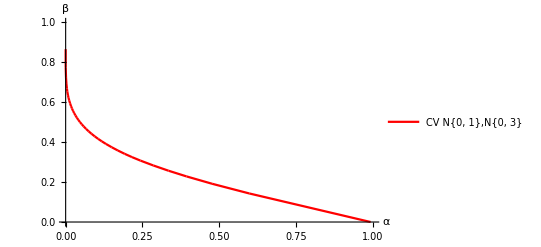
-Graphics--Graphics-

```mathematica
{{pCVNPRNormalPlot,vCVNPRNormalPlotLineValues},vCVNPRNormalSDs}=xCVNPR2Normal[{0,1},{0,3},0.5];
Row[{pCVNPRNormalPlot,
Show[Plot[PDF[NormalDistribution[0,1],x],{x,-5,5},ImageSize->{400,300}],Plot[PDF[NormalDistribution[0,3],x],{x,-5,5},ImageSize->{400,300}]]}]
```

#### Compare to Estimation Without CV

In the graph below, you can see that the Neyman-Pearson lower bounds generated by CV and no CV methods are practically identical. So, no obvious bias was introduced in the CV method. The number of mixture samples in both is 10000. 500 of the samples are used to estimate βMin for the CV method. The maximum number of tangent lines is 50 in both. Not all tangent lines will be used in generating the bound, as described previously.

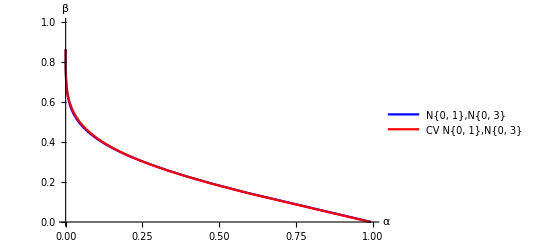

```mathematica
Show[pNPRNormalPlot,pCVNPRNormalPlot]
```

In the following tables, you can see how the means and standard deviations for all ρ(u,v) estimations compare across both methods. Note that the number of tangent lines generated by each method can be different, so comparing across rows may not be as clear for every simulation. As explained previously, the columns are sorted by decreasing x-intercept, but for the CV standard deviations, this does always not result in decreasing standard deviations as it does for the no CV standard deviations. The CV means are slightly lower for all estimations. So, a very slight bias is present. In one simulation, the standard deviations decreased by 70% at most, to 6% at the least. As the standard deviation in the no CV method decreased, the introduction of a CV was consistently less and less effective at decreasing the standard deviation.

```mathematica
Row[{
Column[Prepend[vNPRNormalPlotLineValues[[All,3,3]],"Means, No CV"],Dividers->All],
" ",
Column[Prepend[vCVNPRNormalPlotLineValues[[All,3,3]],"Means, CV"],Dividers->All],
" ",
Column[Prepend[vNPRNormalPlotLineValues[[All,3,4]],"Std Dev, No CV"],Dividers->All],
" ",
Column[Prepend[vCVNPRNormalPlotLineValues[[All,3,4]],"Std Dev, CV"],Dividers->All],
" "
}]
```

Means, No CV
0.259912
0.268709
0.274309
0.277579
0.278923
0.278882
0.277501
0.275052
0.271735
0.267702
0.263011
0.25769
0.251761
0.245353
0.238468
0.231181
0.22347
0.215374
0.206927
0.198158
0.189111
0.17973
0.170023
0.160012
0.14971
0.139138
0.128308
0.117209
0.105836
0.0941687
0.0821813
0.0698541
0.0571813
0.0440853
0.0304824
0.0162535
0.000865624 Means, CV
0.259326
0.268429
0.274143
0.277458
0.279028
0.279071
0.277786
0.275603
0.27262
0.268858
0.264366
0.25916
0.253437
0.247219
0.240531
0.233377
0.225776
0.217785
0.209375
0.200625
0.191556
0.182168
0.172446
0.162397
0.152033
0.141387
0.130425
0.11917
0.107557
0.0956341
0.0833804
0.0708128
0.0578735
0.04457
0.0307847
0.0163709
0.000866024 Std Dev, No CV
0.00541931
0.0053264
0.00521191
0.00508364
0.00494505
0.00480031
0.00464979
0.00449534
0.00433827
0.00417958
0.00401962
0.00385853
0.00369638
0.00353392
0.00337113
0.00320844
0.0030457
0.00288311
0.00272085
0.00255908
0.00239813
0.00223772
0.00207788
0.00191875
0.00176042
0.00160307
0.00144688
0.00129196
0.00113846
0.000986543
0.000836366
0.00068815
0.000542402
0.00039961
0.000260534
0.000126857
4.80389×10^-6 Std Dev, CV
0.00156126
0.0016528
0.00174295
0.00181909
0.00187595
0.00191669
0.00194618
0.00195909
0.00195814
0.00194692
0.00193197
0.00191014
0.00188453
0.00185382
0.00181607
0.00177286
0.00172258
0.00166651
0.00161123
0.00155341
0.00148781
0.00141563
0.00134412
0.00126914
0.00118928
0.00110692
0.00101752
0.000919138
0.000819809
0.000718865
0.000614997
0.000513094
0.000411716
0.000309171
0.000206475
0.000104973
4.56579×10^-6